# HydrogenWavefunction

The position-space wavefunction of the hydrogen atom

## Definition

```mathematica
HydrogenWavefunction[{n_Integer?Positive,l_Integer?NonNegative,m_Integer},a_,{r_,θ_,ϕ_},Z_Integer:1]/;Abs[m]≤l<n:=With[{ρ=(2Z r)/(n a)},√(((2Z)/(n a))^3((n-l-1)!)/(2n(n+l)!))Exp[-ρ/2] ρ^l LaguerreL[n-l-1,2l+1,ρ]SphericalHarmonicY[l,m,θ,ϕ]]
```

## Documentation

### Usage

HydrogenWavefunction[{n,l,m},a,{r,θ,ϕ}]

gives the wavefunction for the hydrogen atom with quantum numbers (n, l, m) and Bohr radius a as a function of the spherical coordinates r, θ and ϕ.

HydrogenWavefunction[{n,l,m},a,{r,θ,ϕ},Z]

gives the hydrogen-like wavefunction with nuclear charge Z.

### Details & Options

Additional information about usage and options.

## Examples

### Basic Examples

The hydrogen ground state wavefunction:

```mathematica
HydrogenWavefunction[{1,0,0},a,{r,θ,ϕ}]
```

(√(1/a^3) ⅇ^(-r/a))/(√π)

The squared magnitude of the wavefunction gives the probability distribution for finding the electron:

```mathematica
Simplify[Abs[HydrogenWavefunction[{3,1,-1},a,{r,θ,ϕ}]]^2,a>0&&r>0&&0<ϕ<π&&0<θ<2π]
```

(ⅇ^(-(2 r)/(3 a)) r^2 (-6 a+r)^2 Sin[θ]^2)/(6561 a^7 π)

### Scope

Plot radial dependence of a few wavefunctions:

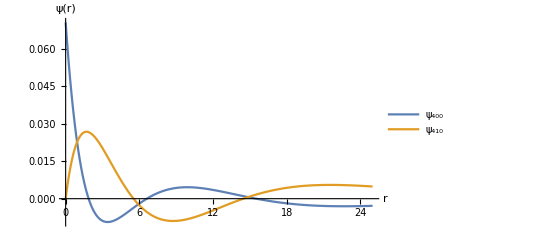

```mathematica
With[{a=1},Plot[Evaluate[Re/@{HydrogenWavefunction[{4,0,0},a,{r,0,ϕ}],HydrogenWavefunction[{4,1,0},a,{r,0,ϕ}]}],{r,0,25},]]
```

Plot the polar dependence of one wavefunction at various radii:

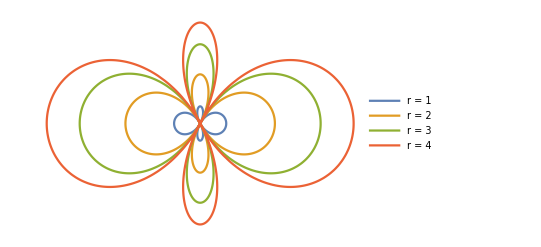

```mathematica
With[{a=1},PolarPlot[Evaluate[Table[Re@HydrogenWavefunction[{3,2,0},a,{r,θ,0}],{r,4}]],{θ,0,2π},]]
```

Plot the electron probability density for various wavefunctions:

```mathematica
With[{a=1},Table[DensityPlot[Abs[HydrogenWavefunction[{3,l,0},a,{x^2+y^2,ArcTan[x,y],0}]]^2,{x,-5,5},{y,-5,5},],{l,0,2}]]
```

-Graphics-

### Properties and Relations

Verify the orthogonality property of HydrogenWavefunction:

```mathematica
Assuming[a>0,∫_0^(2π) ∫_0^π ∫_0^∞ Conjugate[HydrogenWavefunction[{3,2,1},a,{r,θ,ϕ}]]HydrogenWavefunction[{3,2,-1},a,{r,θ,ϕ}] r^2 Sin[θ]ⅆrⅆθⅆϕ]
```

0

Verify the normalization property of HydrogenWavefunction:

```mathematica
Assuming[a>0,∫_0^(2π) ∫_0^π ∫_0^∞ Abs[HydrogenWavefunction[{3,2,0},a,{r,θ,ϕ}]]^2 r^2 Sin[θ]ⅆrⅆθⅆϕ]
```

1

Verify that HydrogenWavefunction satisfies the time-independent Schrödinger equation:

```mathematica
With[{n=3,l=2,m=-1},
ψ=HydrogenWavefunction[{n,l,m},a,{r,θ,ϕ}];Simplify[-ℏ^2/(2μ)Laplacian[ψ,{r,θ,ϕ},"Spherical"]-ℯ^2/(4π Subscript[ε, 0] r)ψ==-ℏ^2/(2μ a^2 n^2)ψ/.a->(4π Subscript[ε, 0] ℏ^2)/(μ ℯ^2)]]
```

True

Show a change of nuclear charge:

```mathematica
Grid[{#,HydrogenWavefunction[{1,0,0},a,{r,θ,ϕ},#]}&/@{1,2}, Frame-> All]
```

1 | (√(1/a^3) ⅇ^(-r/a))/(√π)
2 | 2 √(1/a^3) ⅇ^(-(2 r)/a) √(2/π)

### Neat Examples

Plot hydrogen orbital densities:

```mathematica
With[{a0=Quantity["BohrRadius"]/Quantity["Meters"],n=2,l=1,m=0},DensityPlot3D[Abs[HydrogenWavefunction[{n,l,m},a0,{√(x^2+y^2+z^2),ArcTan[z,√(x^2+y^2)],ArcTan[x,y]}]]^2,{x,-5 a0,5 a0},{y,-5 a0,5 a0},{z,-5 a0,5 a0},PlotLegends->Automatic]]
```

-Graphics3D-

## Source & Additional Information

### Contributed By

Matt Kafker

### Keywords

Quantum Mechanics

Hydrogen

Wavefunction

Orbitals

### Categories

3D Visualization |  Accessibility
 Array Manipulation |  Cloud & Deployment
 Core Language & Structure |  Data Manipulation & Analysis
 Engineering Data & Computation |  External Interfaces & Connections
 Financial Data & Computation |  Geographic Data & Computation
 Geometry |  Graphs & Networks
 Higher Mathematical Computation |  Images
 Just For Fun |  Knowledge Representation & Natural Language
 Machine Learning |  Notebook Documents & Presentation
 Programming Utilities |  Repository Tools
 Scientific and Medical Data & Computation |  Social, Cultural & Linguistic Data
 Sound & Video |  Strings & Text
 Symbolic & Numeric Computation |  System Operation & Setup
 Time-Related Computation |  User Interface Construction
 Visualization & Graphics |  Wolfram Physics Project

### Related Symbols

LaguerreL

SphericalHarmonicY

### Related Resource Objects

SolidHarmonicR

SolidHarmonicI

WignerMatrix

### Source/Reference Citation

Tam, Patrick T. A Physicist’s Guide to Mathematica. 2nd ed., Elsevier/Academic Press, 2008.

### Links

Link to other related material

### Tests

MyFunction[2.64589×10^-10,2.64589×10^-10]

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session |  ScriptScript run in batch mode |  SubkernelParallel or grid subkernel
 WebEvaluationCloud evaluation initiated by an HTTP request |  WebAPIAPI called through an HTTP request |  ScheduledScheduled task
 BatchJobRemote batch job |  |

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.